# Script for SXS vs BoB comparison with Ωisco from FinalSpinMassQNM.nb and Ωi=Ωisco

## to accompany https://arxiv.org/abs/2203.08998

Author: Maria Babiuc-Hamilton and Dillon Buskirk

```mathematica
ClearAll["Global`*"];Off[General::spell];Remove["Global`*"]
SetOptions[Simplify,TimeConstraint->1000];
$Assumptions=η>0 &&t∈Reals;
Unprotect[Sqrt]; Sqrt[x_^2]:=x; Protect[Sqrt];
$MinPrecision=20; (* $MachinePrecision;*)
```

Initial and final parameters

From FinalSpinMassQNM.nb,  values for equal non-spinning binaries χf0Meq and Mfχ0Meq

```mathematica
m1 =0.5000000618087954; m2=1-m1;
q=m1/m2; M=m1+m2; μ=(m1*m2)/M;η=μ/M;
γ=0.5772156649;
```

#Tune to SXS 0746

```mathematica
χf=0.880726115;
Mf=0.918682416261;
```

We take the mean value for frequency and Q from FinalSpinMassQNM.nb,  for l=2, m=2 mode:

```mathematica
MfωQNM = 0.6566451157454446;
QQNM=5.003059966404495;
ωQNM=MfωQNM/Mf
τ = 2 QQNM/ωQNM
```

0.714768

13.9991

Freely chosen parameters

```mathematica
Ap=1;R=1;tp=0;
```

Starting BOB formulation

Quick check: Ωisco from FinalSpinMassQNM.nb, 1611.00332 eqs. (2)a,b,c and (3)a,b,c

```mathematica
Ωisco=(-0.091933*χf+0.097593)/(χf^2-2.4228*χf+1.4366) 
ωqnm=1.5251-1.1568*(1-χf)^0.1292
```

0.211907

0.646183

Values taken directly from EccInsMerger_q1e0001.

```mathematica
x3PNISCO =0.178329;
r3PNISCO = 4.83849;
Ω3OrbPNISCO = 0.075297;
Ω3OrbPNISCOdot = 8.57723 10^-4 ;
Ω3PN = 2 Ω3OrbPNISCO
Ω3PNdot = 2 Ω3OrbPNISCOdot;
```

0.150594

Clearly, the value of the ISCO frequency comes underestimated from the PN model, because we do not take into account the spin of the individual bhs. While the resonance frequency might be overestimated by the analytic fit.

Now we can implement the BoB

```mathematica
Ωi = Ωisco (*Ω3OrbPNISCO*)
Ωidot = Ω3OrbPNISCOdot;
tp =0;
ΩQNM = ωQNM/2
```

0.211907

0.357384

```mathematica
0.21242
```

0.21242

```mathematica
ti=tp-τ/2 Log[(ΩQNM^4-Ωi^4)/(2*τ*Ωi^3 Ωidot)-1]
```

-28.8388

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

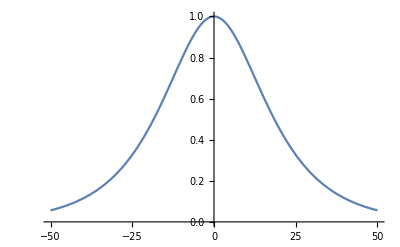

```mathematica
ψ4[t_]:=Ap*Sech[(t-tp)/τ];
Plot[ψ4[t],{t,-50,50}]
```

```mathematica
kB=((ΩQNM^4-Ωi^4)/(1-Tanh[(ti-tp)/τ]))
```

0.00726454

```mathematica
ΩB[t_]:=(Ωi^4+kB(Tanh[(t-tp)/τ]-Tanh[(ti-tp)/τ]))^(1/4)
```

```mathematica
ωBoB[t_]:=2*ΩB[t];
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

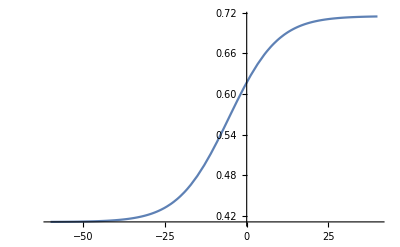

```mathematica
Plot[ωBoB[t],{t,-60,40}]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

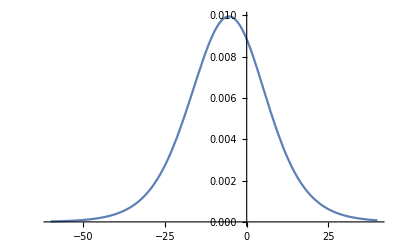

```mathematica
Plot[ωBoB'[t],{t,-60,40}]
```

```mathematica
FindRoot[ωBoB''[t]==0,{t,-40,0}]
```

{t→-5.43115}

```mathematica
tfBoB= -5.431151848927049
```

-5.43115

```mathematica
Kappap=(Ωi^4+kB(1-Tanh[(ti-tp)/τ]))^(1/4)
```

0.357384

```mathematica
Kappam=(Ωi^4-kB(1+Tanh[(ti-tp)/τ]))^(1/4)
```

0.205523

```mathematica
arctanp[t_]:=Kappap*τ*(ArcTan[(ΩB[t]/Kappap)]-ArcTan[Ωi/Kappap])
arctanm[t_]:=Kappam*τ*(ArcTan[ΩB[t]/Kappam]-ArcTan[Ωi/Kappam])
arctanhp[t_]:=Kappap*τ*(ArcTanh[ΩB[t]/Kappap]-ArcTanh[Ωi/Kappap])
arctanhm[t_]:=Kappam*τ*(ArcTanh[ΩB[t]/Kappam]-ArcTanh[Ωi/Kappam])
```

```mathematica
PhaseB[t_]:=arctanp[t]+arctanhp[t]-arctanm[t]-arctanhm[t]
```

```mathematica
ϕBoB[t_]:=2*PhaseB[t]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

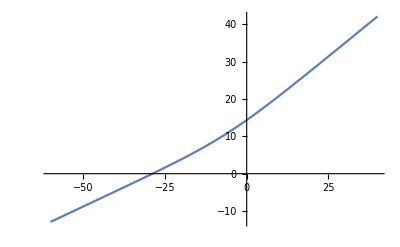

```mathematica
Plot[ϕBoB[t],{t,-60,40}]
```

```mathematica
AmpBoB[t_]:=Abs[ψ4[t]]/ωBoB[t]^2
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

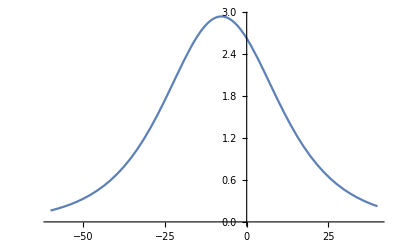

```mathematica
Plot[AmpBoB[t],{t,-60,40}]
```

```mathematica
FindMaximum[AmpBoB[t],t]
```

{2.94181,{t→-7.74506}}

```mathematica
tpBoB=-7.745060725971462
```

-7.74506

```mathematica
AmpBoBMax=MaxValue[AmpBoB[t],t]
```

2.94181

```mathematica
hBoB[t_]:=AmpBoB[t]*Exp[-ⅈ*ϕBoB[t]]
```

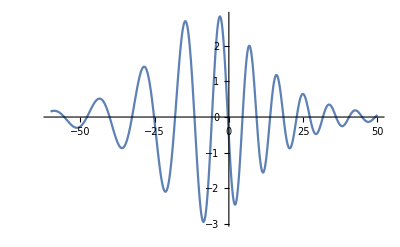

```mathematica
Plot[Re[hBoB[t]],{t,-60,50}]
```

```mathematica
FindMaximum[{Re[hBoB[t]],-40<=t<=0},{t,-3}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{2.81807,{t→-3.01077}}

```mathematica
FindMinimum[{Re[hBoB[t]],-40<=t<=0},{t,-8}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{-2.93821,{t→-8.54177}}

```mathematica
FindMaximum[{Re[hBoB[t]],-40<=t<=0},{t,-15}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{2.68555,{t→-14.6432}}

```mathematica
thBoB =-8.541766646992949;
```

```mathematica
MaxRehBoB=-2.9382109674919925;
```

```mathematica
RehBoBshifted=Re[hBoB[t+thBoB ]]/MaxRehBoB;
```

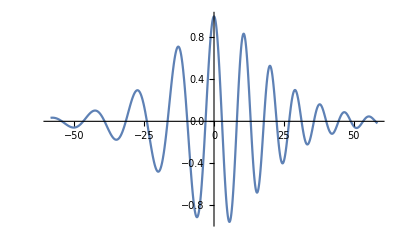

```mathematica
Plot[RehBoBshifted,{t,-50+thBoB,50-thBoB}]
```

```mathematica
Δtf = tfBoB-tpBoB
```

2.31391

```mathematica
Δth = thBoB-tpBoB
```

-0.796706

```mathematica
SXS0746Data=Import["/Users/dillonbuskirk/Dropbox/Dillon/GradWork/Code/Data/SXS_BBH_0746_N4_Y_l2_m2.txt","Table","FieldSeparators"->","]
```

{{-107.805,-0.000106162,-0.00278313},{-106.865,-0.000102975,-0.0027943},{-105.924,-0.000105747,-0.00280808},{-104.983,-0.000112972,-0.00281719},16649,{5233.8,-0.0000241046,2.811×10^-6},{5233.9,-0.0000223141,3.95057×10^-6},{5234,-0.0000204591,4.94743×10^-6},{5234.1,-0.0000185512,5.81771×10^-6}}
 |  |  |  |

```mathematica
(*SXS0746Data=Import["/Users/babiuc/Dropbox/StudentResearch/Dillon/GradWork/Code/Data/SXS_BBH_0746_N4_Y_l2_m2.txt","Table","FieldSeparators"->","]*)
```

```mathematica
(*SXS0746Data=Import["/Users/dillonbuskirk/Dropbox/Dillon/GradWork/Code/Data/SXS_BBH_0746_N4_Y_l2_m2.txt","Table","FieldSeparators"->","];*)
```

```mathematica
SXS0746DataTime=SXS0746Data[[All,1]];
```

```mathematica
ReSXS0746DataStrain=SXS0746Data[[All,2]];
```

```mathematica
MaxReSXS0746DataStrain=Max[ReSXS0746DataStrain]
```

0.386693

```mathematica
MinReSXS0746DataStrain=Min[ReSXS0746DataStrain]
```

-0.37401

```mathematica
ImSXS0746DataStrain=SXS0746Data[[All,3]];
```

```mathematica
MaxImSXS0746DataStrain=Max[ImSXS0746DataStrain]
```

0.383055

```mathematica
MinImSXS0746DataStrain=Min[ImSXS0746DataStrain]
```

-0.382347

```mathematica
AmpSXS0746DataStrain = Sqrt[ReSXS0746DataStrain^2+ImSXS0746DataStrain^2];
```

```mathematica
MaxAmpSXS0746DataStrain=Max[Abs[AmpSXS0746DataStrain]]
```

0.386724

```mathematica
Position[ReSXS0746DataStrain ,_?(#>0.999999*MaxReSXS0746DataStrain&)]
```

{{15238}}

```mathematica
Position[AmpSXS0746DataStrain ,_?(#>0.999999*MaxAmpSXS0746DataStrain&)]
```

{{15238}}

```mathematica
SXS0746DataTimeShift=SXS0746DataTime-SXS0746DataTime[[15238]];
```

```mathematica
AmpSXS0746DataStrainNorm = AmpSXS0746DataStrain/MaxAmpSXS0746DataStrain;
```

```mathematica
AmpSXS0746DataShift=Transpose[{SXS0746DataTimeShift,AmpSXS0746DataStrainNorm }];
```

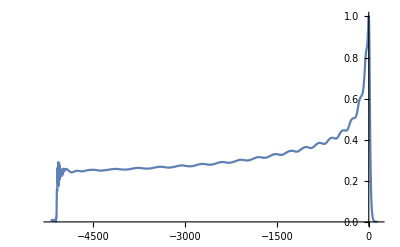

```mathematica
ListPlot[AmpSXS0746DataShift[[All,1;;2]],Joined->True]
```

```mathematica
ReSXS0746DataStrainNorm = ReSXS0746DataStrain/MaxAmpSXS0746DataStrain;
ImSXS0746DataStrainNorm = ImSXS0746DataStrain/MaxAmpSXS0746DataStrain;
```

```mathematica
pReSXS0746DataShift=Transpose[{SXS0746DataTimeShift,+ReSXS0746DataStrainNorm}];
```

```mathematica
mReSXS0746DataShift=Transpose[{SXS0746DataTimeShift,-ReSXS0746DataStrainNorm }];
```

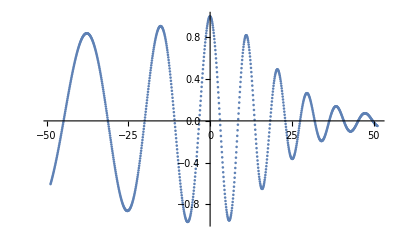

```mathematica
ListPlot[pReSXS0746DataShift[[14750;;15750]]]
```

tfBoB, tpBoB, thBoB

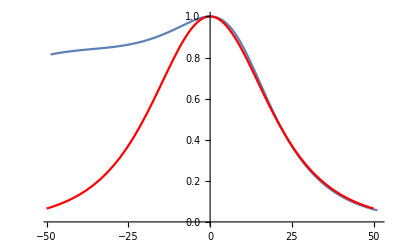

```mathematica
Show[ListPlot[AmpSXS0746DataShift[[14750;;15750]],Joined->True],Plot[AmpBoB[t+tpBoB]/AmpBoBMax,{t,-50,50},PlotStyle->Red]]
```

```mathematica
tfBoB
 tpBoB
 thBoB
```

-5.43115

-7.74506

-8.54177

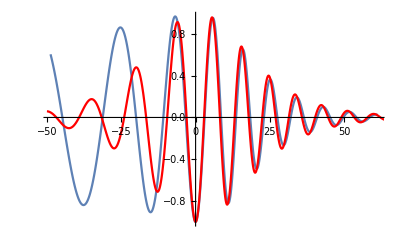

```mathematica
Show[ListPlot[mReSXS0746DataShift[[14750;;15850]],Joined->True],
Plot[Re[hBoB[t+thBoB]]/AmpBoBMax,{t,-50,70},PlotStyle->Red]]
```

```mathematica
ArgSXS= Flatten[ArcTan[ImSXS0746DataStrainNorm/ReSXS0746DataStrainNorm]];
```

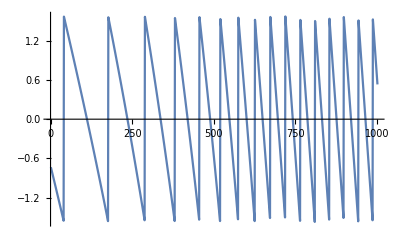

```mathematica
ListPlot[ArgSXS[[14750;;15750]],Joined->True]
```

Function taken from https://community.wolfram.com/groups/-/m/t/1340126

```mathematica
Unwrap[lst_List]:=Unwrap[lst,2Pi] (*phase jumps of 2Pi is the default because of trigonometric funtions*)
Unwrap[lst_List,Δ_]:=Unwrap[lst,Δ,Scaled[0.5]] (*default tolerance is half the phase jump Δ*)
Unwrap[lst_List,Δ_,tolerance_]:=Module[{tol,jumps},tol=If[Head[tolerance]===Scaled,Δ tolerance[[1]],tolerance];
jumps=Differences[lst];
jumps=-Sign[jumps]Unitize[Chop[Abs[jumps],tol]];
jumps=Δ Prepend[Accumulate[jumps],0];
jumps+lst]
```

```mathematica
unwrapArgSXS=Unwrap[ArgSXS,3];
```

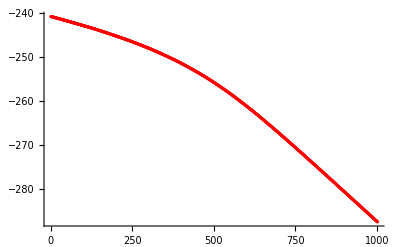

```mathematica
unwrapArgSXSFiltered=MeanFilter[unwrapArgSXS,100];
ListPlot[unwrapArgSXSFiltered[[14750;;15750]],PlotStyle->Red]
```

```mathematica
ϕSXS=Transpose[{SXS0746DataTimeShift,Flatten[-unwrapArgSXS]}];
ϕSXSfiltered=Transpose[{SXS0746DataTimeShift,Flatten[-unwrapArgSXSFiltered]}];
```

```mathematica
interpϕSXS=Interpolation[ϕSXS[[14700;;15800]],InterpolationOrder->4]
interpϕSXSfiltered=Interpolation[ϕSXSfiltered[[14700;;15800]],InterpolationOrder->4]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

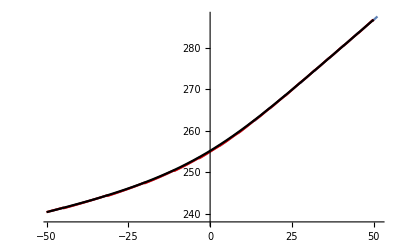

```mathematica
Show[ListPlot[ϕSXS[[14750;;15750]],Joined->True],Plot[interpϕSXS[t],{t,-50,50},PlotStyle->Red], Plot[interpϕSXSfiltered[t],{t,-50,50},PlotStyle->Black]]
```

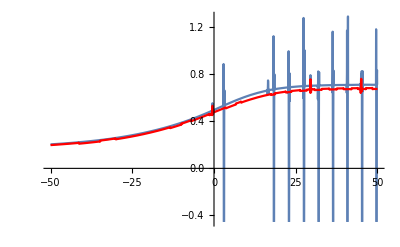

```mathematica
Show[Plot[interpϕSXS'[t],{t,-50,50}],Plot[interpϕSXSfiltered'[t],{t,-50,50},PlotStyle->Red]]
```

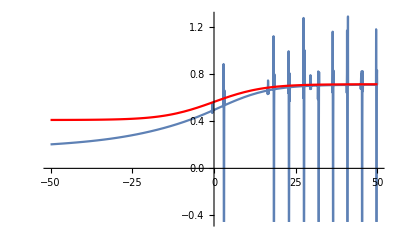

```mathematica
Show[Plot[interpϕSXS'[t],{t,-50,50}],Plot[ωBoB[t+tfBoB],{t,-50,50},PlotStyle->Red]]
```

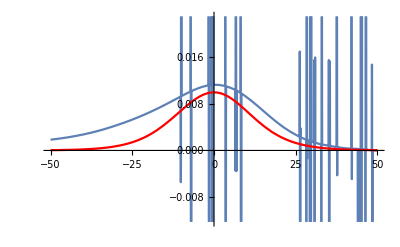

```mathematica
Show[Plot[interpϕSXSfiltered''[t],{t,-50,50}],Plot[ωBoB'[t+tfBoB],{t,-50,50},PlotStyle->Red]]
```

```mathematica
ΔϕSXSBoB =interpϕSXS[0]-Re[ϕBoB[0]]
```

240.661

```mathematica
ΔϕSXSBoBfiltered =interpϕSXSfiltered[0]-Re[ϕBoB[tfBoB]]
```

244.061

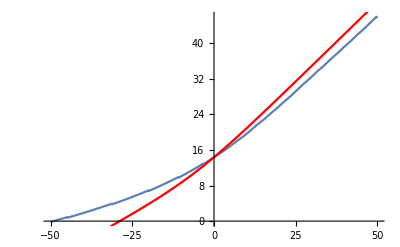

```mathematica
Show[Plot[interpϕSXS[t]-ΔϕSXSBoB,{t,-50,50}],Plot[ϕBoB[t],{t,-50,50},PlotStyle->Red]]
```

Plots for paper: SXS-BoB comparison

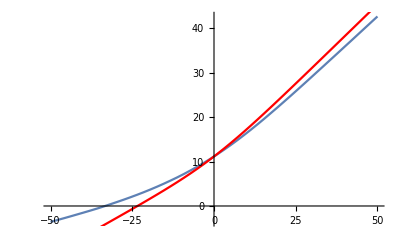

```mathematica
Show[Plot[interpϕSXSfiltered[t]-ΔϕSXSBoBfiltered,{t,-50,50}],Plot[ϕBoB[t+tfBoB],{t,-50,50},PlotStyle->Red]]
```

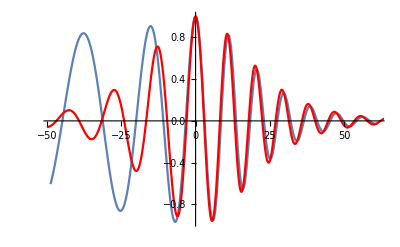

```mathematica
Show[ListPlot[pReSXS0746DataShift[[14750;;15850]],Joined->True],
Plot[-Re[hBoB[t+thBoB]]/AmpBoBMax,{t,-50,70},PlotStyle->Red]]
```

```mathematica
Show[ListPlot[AmpSXS0746DataShift[[14750;;15750]],Joined->True],Plot[AmpBoB[t+tpBoB]/AmpBoBMax,{t,-50,50},PlotStyle->Red]]
```

-Graphics-

## Plotting Work

```mathematica
dt=0.01;
```

```mathematica
tArray=Table[t,{t,-50,50,dt}];
```

```mathematica
tArray1=Table[t,{t,-50,70,dt}];
```

```mathematica
AmpBoBTab=Table[AmpBoB[t+tpBoB]/AmpBoBMax,{t,-50,50,dt}];
```

```mathematica
AmpBoBvsTimeTab=Partition[Riffle[tArray,AmpBoBTab],2];
```

```mathematica
PrependTo[AmpBoBvsTimeTab, {"t(M)", "hAmp(t)"}];
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/AmpBoBforSXScomp.txt",AmpBoBvsTimeTab]*)
```

```mathematica
SXSAmpData=AmpSXS0746DataShift[[14750;;15750]];
```

```mathematica
PrependTo[SXSAmpData, {"t(M)", "hAmp(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/AmpSXSforSXScomp.txt",SXSAmpData]
```

dropbox/dillon/paperplottingwork/AmpSXSforSXScomp.txt

```mathematica
hBoBTab=Table[Re[hBoB[t+thBoB]]/AmpBoBMax,{t,-50,70,dt}];
```

```mathematica
hBoBvsTimeTab=Partition[Riffle[tArray1,hBoBTab],2];
```

```mathematica
PrependTo[hBoBvsTimeTab, {"t(M)", "h(t)"}];
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hBoBforSXScomp.txt",hBoBvsTimeTab]*)
```

```mathematica
SXShData=mReSXS0746DataShift[[14750;;15850]];
```

```mathematica
PrependTo[SXShData, {"t(M)", "h(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/hSXSforSXScomp.txt",SXShData]
```

dropbox/dillon/paperplottingwork/hSXSforSXScomp.txt

```mathematica
BoBphasetab=Table[ϕBoB[t+tfBoB],{t,-50,50,dt}];
```

```mathematica
BoBphasevstimetab=Partition[Riffle[tArray,BoBphasetab],2];
```

```mathematica
PrependTo[BoBphasevstimetab, {"t(M)", "ϕ(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/phiBoBforSXScomp.txt",BoBphasevstimetab]
```

dropbox/dillon/paperplottingwork/phiBoBforSXScomp.txt

```mathematica
SXSphasetab=Table[interpϕSXSfiltered[t]-ΔϕSXSBoBfiltered,{t,-50,50,dt}];
```

```mathematica
SXSphasevstimetab=Partition[Riffle[tArray,SXSphasetab],2];
```

```mathematica
PrependTo[SXSphasevstimetab, {"t(M)", "ϕ(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/phiSXSforSXScomp.txt",SXSphasevstimetab]
```

dropbox/dillon/paperplottingwork/phiSXSforSXScomp.txt